```mathematica
(* This notebook creates the figures for the St. Louis Fed keynote speech. *)
```

```mathematica
(* Set up the environment in which the figure-generating files can be executed *)
ClearAll["Global`*"];ParamsAreSet=False;
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
rootDir = SetDirectory["../../.."];
AutoLoadDir=SetDirectory["./Mathematica/CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
Get[CoreCodeDir<>"/DrawDiagrams.m"];
FigsDir=SetDirectory[rootDir<>"/Examples/FedStLouis/Figures/"];
CodeDir=SetDirectory[rootDir<>"/Examples/FedStLouis"];
VerboseOutput=False;
PlotRangeVertical={-0.5,0.15};
```

```mathematica
(* We use the set of parameter values of ctDiscrete except that Severance = 4; we also incorporate death rate = 0.05.*)
Get[CoreCodeDir<>"/ParametersBase.m"];
(* We calculate the discount rates for patient and impatient people to match debt and asset ratios in 2001. *)
Severance = 4;
PDies = 0.05;
Get[CodeDir<>"/CalDiscRate.m"];
ϑImpatient = CalDiscRate[-2];
ϑPatient=CalDiscRate[12];
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

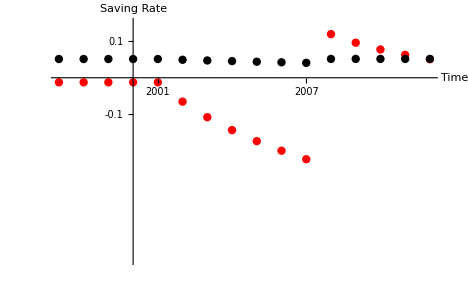

```mathematica
(* Plot saving dynamics over credit cycle. *)

Get[CodeDir<>"/SavPathOverECreditCycleSlow.m"];
Print[Show[SavPathOverECreditCycleSlow]];
```

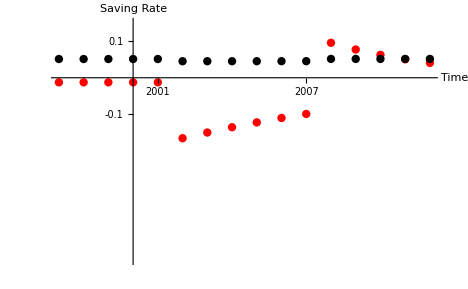

```mathematica
(* Plot saving dynamics over credit cycle. *)

Get[CodeDir<>"/SavPathOverECreditCycle.m"];
Print[Show[SavPathOverECreditCycle]];
```

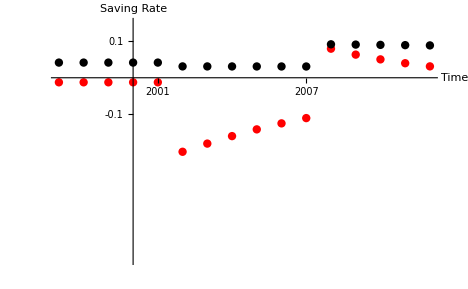

```mathematica
(* Plot Saving dynamics when there is a decrease in unemployment rate expectations then an abrupt reversal of expectation. *)
Get[CoreCodeDir<>"/ParametersBase.m"];
Severance =4;
PDies = 0.05;
Get[CodeDir<>"/CalDiscRate.m"];
ϑImpatient = CalDiscRate[-2];
ϑPatient=CalDiscRate[12];
Get[CodeDir<>"/SavPathOverEUriskCycle.m"];
Print[Show[SavPathOverEUriskCycle]];
```

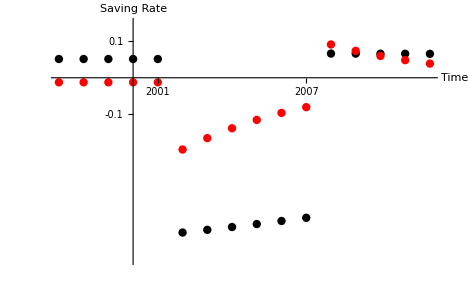

```mathematica
(* Plot saving dynamics when there is an increase of growth expectation then an abrupt reversal of the expectation *)
Get[CoreCodeDir<>"/ParametersBase.m"];
Severance = 4;
PDies = 0.05;
Get[CodeDir<>"/SavPathOverEGrowthCycle.m"];
Print[Show[SavPathOverEGrowthCycle]];
```

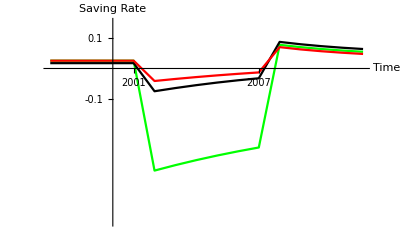

```mathematica
SavPathOverECycles = ShowLegend[Show[SavPathOverEGrowthCycleAll,SavPathOverEUriskCycleAll,SavPathOverECreditCycleAll],{
{{Graphics[{Red,Line[{{0,0},{1,0}}]}]
,"𝔼[ϛ] Cycle (Credit)    "}
,{Graphics[{Black,Line[{{0,0},{1,0}}]}]
,"𝔼[℧] Cycle (Unemp Risk)"}
,{Graphics[{Green,Line[{{0,0},{1,0}}]}]
,"𝔼[Γ] Cycle (Growth)    "}
},
LegendPosition->{-0.1,-0.6},LegendSize->{1.1,0.25}}];
Print[Show[SavPathOverECycles]];
```

```mathematica
Export[FigsDir<>"/SavPathOverECycles.pdf",SavPathOverECycles];
```

```mathematica
SavPathOverECycles = ShowLegend[Show[SavPathOverEGrowthCycleAll,SavPathOverEUriskCycleAll,SavPathOverECreditCycleAll],{
{{Graphics[{Red,Line[{{0,0},{1,0}}]}]
,"𝔼[ϛ] Cycle (Credit)    "}
,{Graphics[{Black,Line[{{0,0},{1,0}}]}]
,"𝔼[℧] Cycle (Unemp Risk)"}
,{Graphics[{Green,Line[{{0,0},{1,0}}]}]
,"𝔼[Γ] Cycle (Growth)    "}
},
LegendPosition->{-0.1,-0.6},LegendSize->{1.1,0.25}}];
Print[Show[SavPathOverECycles]];
```

-Graphics-